## ALP low-energy couplings (following 2110.10698 and 1708.00443)

## Running of SM couplings: α_s, α_t and gauge couplings

```mathematica
αSsolTemp[αS0_,μ0_,μ_,β0_]=αS[μ]/.DSolve[{μ*D[αS[μ],μ]==-β0 αS[μ]^2/(2Pi),αS[μ0]==αS0},αS[μ],μ][[1]]
μ0Val=91;
MASS["t"]=173;
αS0val=0.113;
yt=√2 MASS["t"]/246.;
αT0val=(*yt^2/(4Pi)*)yt^2/(4Pi);
β0["EW","Λ"]=7;
αSsol[μ_]=αSsol[μ_,"EW","Λ"]=αSsolTemp[αS0val,μ0Val,μ,β0["EW","Λ"]];
β0["m_t","EW"]=11-2/3*5;
αSsol[μ_,"m_b","EW"]=αSsolTemp[αS0val,μ0Val,μ,β0["m_b","EW"]];
β0["μ","m_b"]=11-2/3*4;
αSsol[μ_,"μ","m_b"]=αSsolTemp[αS0val,μ0Val,μ,β0["μ","m_b"]];
αTsolTemp=αT/.NDSolve[{μ*D[αT[μ],μ]==αT[μ]/(2Pi)(9/2 αT[μ]-8αSsol[μ]),αT[μ0Val]==αT0val},αT,{μ,MASS["t"],10^12}][[1]];
αTsol[μ_]=αTsolTemp[μ];
Uval[μ_,Λ_]=-1/18*Log[1-9/2 αTsol[μ]/αSsol[μ](1-(αSsol[Λ]/αSsol[μ])^(1/7))];
(*Running from 2105.03419*)
data1=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology/AlphaUY.txt"}],"Table"];
minΛ=data1[[All,1]]//Min;
αUYsol[μ_]=If[μ>=minΛ,Evaluate[10^Interpolation[Log10[data1],InterpolationOrder->1][Log10[μ]]],Evaluate[data1[[1]][[2]]]];
data1=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"phenomenology/AlphaSU2L.txt"}],"Table"];
minΛ=data1[[All,1]]//Min;
αSU2Lsol[μ_]=If[μ>=minΛ,Evaluate[10^Interpolation[Log10[data1],InterpolationOrder->1][Log10[μ]],Evaluate[data1[[1]][[2]]]]];
```

(2 π αS0)/(αS0 β0 log(μ)-αS0 β0 log(μ0)+2 π)

## Effective couplings to photons and gluons

```mathematica
(*Loop factor for the aGG and aγγ couplings*)
LoopFactor[τ_]=1 - τ*Piecewise[{{ArcSin[1/(√τ)]^2,τ>=1},{(Pi/2+I/2 Log[(1+√(1+τ))/(1-√(1-τ))])^2,τ<1}}]
LogPlot[Abs[LoopFactor[(4*1.29^2)/ma^2]],{ma,0.1,2}];
(*Effective coupling of the ALP to photons and gluons - loop part*)
cGGeff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,quarklist_]:=Sum[Symbol["c"<>q]*LoopFactor[(4*MASS[q]^2)/ma^2],{q,quarklist}]
cGGtest1[ma_,cu_,cd_,cs_,cc_,cb_,ct_]=cGGeff[ma,cu,cd,cs,cc,cb,ct,{"u","d","s","c","b","t"}];
cGGtest2[ma_,cu_,cd_,cs_,cc_,cb_,ct_]=cGGeff[ma,cu,cd,cs,cc,cb,ct,{"c","b","t"}];
LogLogPlot[{Abs[cGGtest1[ma,1,1,1,1,1,1]],Abs[cGGtest2[ma,1,1,1,1,1,1]]},{ma,0.1,2}];
(*Photon coupling*)
(*Loop part from the gluon coupling. Eq. 16 from https://arxiv.org/pdf/1708.00443*)
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,Λ_,"Loop c_G"]=-3cG αsData[ma]^2/Pi^2*Sum[CHARGE[q]^2 LoopFactor[(4*MASS[q]^2)/ma^2]Log[(Λ/If[MemberQ[{"u","d"},q]==True,MASS["π^0"],If[MemberQ[{"s"},q]==True,MASS["K^+"],MASS[q]]])^2],{q,{"u","d","s","c","b","t"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_(q, all)"]=2*Sum[Symbol["c"<>q]*CHARGE[q]^2 3*LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"u","d","s","c","b"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_(q, heavy)"]=2*Sum[Symbol["c"<>q]*CHARGE[q]^2 3*LoopFactor[(4*MASS[q]^2)/ma^2],{q,{"c","b"}}];
cγγEff[ma_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,"Loop c_l"]=2*Sum[Symbol["c"<>l]*CHARGE[l]^2 LoopFactor[(4*MASS[l]^2)/ma^2],{l,{"e","μ","τ"}}];
```

1-τ (Piecewise[{{(sin^-1(1/(√τ)))^2, τ≥1}, {(1/2 ⅈ log((√(τ+1)+1)/(1-√(1-τ)))+π/2)^2, τ<1}}])

## Running of flavor-diagonal couplings

### Definitions

```mathematica
couplingslist={(4*Pi*αTsol[μ]),αSsol[μ]^2,αSU2Lsol[μ]^2,αUYsol[μ]^2};
coefs["cG"]={2/(8 Pi^2),6/Pi^2,27/(16 Pi^2),11/(16 Pi^2)}couplingslist;
coefs["cW"]={(3*2)/(32 Pi^2),9/(2 Pi^2),27/(8 Pi^2),3/(8 Pi^2)}couplingslist;
coefs["cB"]={(17*2)/(96 Pi^2),11/(2 Pi^2),9/(8 Pi^2),95/(24 Pi^2)}couplingslist;
coefs["ct"]={9/(16 Pi^2),1/2 2/Pi^2,1/2 9/(16 Pi^2),1/2 17/(48 Pi^2)}couplingslist;
coefskeys=Keys[DownValues@coefs][[All,1,1]]
couplingsList[μ_]={RunningCoupling["ct",μ_],RunningCoupling["cG",μ_],RunningCoupling["cW",μ_],RunningCoupling["cB",μ_]}={CT[μ],CGG[μ],CWW[μ],CBB[μ]};
Do[cXXrunning[coef,μ_]=Evaluate[coefs[coef]]*couplingsList[μ]//Total,{coef,coefskeys}];
Nc=3;
cΛ["cG",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cG+cu+cd+cs+cc+cb+ct;
cΛ["cW",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cW+Nc/4*(cu+cd+cs+cc+cb+ct)+1/2(ce+cμ+cτ);
cΛ["cB",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=cB+2*Nc((2/3)^2(cu+cc+ct)+(1/3)^2(cb+cs+cd))-3/2*(cu+cc+ct)+3/2(ce+cμ+cτ);
cΛ["ct",cG_,cW_,cB_,cu_,cd_,cs_,cc_,cb_,ct_,ce_,cμ_,cτ_]=ct;
cGcWcBctFlowTemp[Λ_,cu_,cd_,cs_,cc_,cb_,ct_,cG_,ce_,cμ_,cτ_,cW_,cB_]:=Block[{},
NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,cτ]},{coef,coefskeys}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"]//N,Λ}]
]
(*Running of Subscript[c, q!=t], Subscript[c, l]*)
β03=7;
(*the 2nd and 3rd terms: running from Λ to the top mass*)
(*the last term: running from top mass to μ = 2 GeV*)
cuRunning[Λ_,cu_,ct_,cG_,cd_,cs_,cc_,cb_]=cu-3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
cdRunning[Λ_,cd_,ct_,cG_,cu_,cs_,cc_,cb_]=cd+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
csRunning[Λ_,cs_,ct_,cG_,cu_,cd_,cc_,cb_]=cs+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
ccRunning[Λ_,cc_,ct_,cG_,cu_,cd_,cs_,cb_]=cc-3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi-0.01(3/2*cΛ["cG",cG,cW,cB,cu,cd,cs,cc,cb,ct,ce,cμ,0]-1.4ct-0.6*cb);
cbRunning[Λ_,cb_,ct_,cG_]=cb+3*αTsol[MASS["t"]]/αSsol[MASS["t"]]*5/6*(1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct-1/2(4cG)/β03(αSsol[MASS["t"]]-αSsol[Λ])/Pi;
ceRunning[Λ_,ce_,ct_]=ce+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
cμRunning[Λ_,cμ_,ct_]=cμ+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
cτRunning[Λ_,cτ_,ct_]=cτ+3*αTsol[MASS["t"]]/αSsol[MASS["t"]](1-(αSsol[Λ]/αSsol[MASS["t"]])^(1/7))ct;
ALPcouplingsRGflow[model_,Λ_]:=Module[{value},
Do[value[ALPcouplingslist[[i]]]=couplingPattern[model,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
sols=NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]},{coef,coefskeys}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"],Λ}][[1]];
RGflowTemp["ct"]=CT/.sols;
RGflow["ct"]=RGflowTemp["ct"][MASS["t"]];
RGflow["cW"]=value["cW"];
RGflow["cB"]=value["cB"];
RGflow["cG"]=value["cG"];
RGflow["cu"]=cuRunning[Λ,value["cu"],value["ct"],value["cG"],value["cd"],value["cs"],value["cc"],value["cb"]];
RGflow["cd"]=cdRunning[Λ,value["cd"],value["ct"],value["cG"],value["cu"],value["cs"],value["cc"],value["cb"]];
RGflow["cs"]=csRunning[Λ,value["cs"],value["ct"],value["cG"],value["cu"],value["cd"],value["cc"],value["cb"]];
RGflow["cc"]=ccRunning[Λ,value["cc"],value["ct"],value["cG"],value["cu"],value["cd"],value["cs"],value["cb"]];
RGflow["cb"]=cbRunning[Λ,value["cb"],value["ct"],value["cG"]];
RGflow["ce"]=ceRunning[Λ,value["ce"],value["ct"]];
RGflow["cμ"]=cμRunning[Λ,value["cμ"],value["ct"]];
RGflow["cτ"]=cτRunning[Λ,value["cτ"],value["ct"]];
Table[RGflow[coupling],{coupling,ALPcouplingslist}]
]
```

{cB,cG,ct,cW}

### RG flow computation/importing

```mathematica
ΛlistInt=Table[10^x,{x,Log10[MASS["t"]//N],Log10[10^9.],(Log10[10^9.]-Log10[MASS["t"]])/230}];
(*rgflowcomputoption=dropdownDialog[{"Generate","Import"},"Generate the RG flow of the ALP couplings, or just import it (if it has been generated once)?"];*)
(*rgflowcomputoption="Import";*)
fileRG=FileNameJoin[{NotebookDirectory[]//ParentDirectory,"Temporary data/RGflowModels.m"}];
If[!FileExistsQ[fileRG],
Do[
rgflowlist[model]=Table[Join[{Λ},ALPcouplingsRGflow[model,Λ]],{Λ,ΛlistInt}];
Do[
cRGval[model,Λ_,ALPcouplingslist[[i]]]=Interpolation[rgflowlist[model][[All,{1,i+1}]],InterpolationOrder->1][Λ];
,{i,1,Length[ALPcouplingslist],1}];
tableValuesReplacement[model,Λ_]=Table[ALPcouplingsSymbols[[i]]->cRGval[model,Λ,ALPcouplingslist[[i]]]
,{i,1,Length[ALPcouplingsSymbols],1}];
,{model,ModelListAll}];
TabRGexport=Flatten[Table[{model,ALPcouplingslist[[i]],cRGval[model,Λ,ALPcouplingslist[[i]]]},{model,ModelListAll},{i,1,Length[ALPcouplingslist],1}],1];
Export[fileRG,TabRGexport,"MX"];
,
TabRGimport[Λ_]=Import[fileRG,"MX"];
Do[cRGval[TabRGimport[Λ][[i]][[1]],Λ_,TabRGimport[Λ][[i]][[2]]]=TabRGimport[Λ][[i]][[3]],{i,1,Length[TabRGimport[Λ]],1}]
]
Do[tableValuesReplacement[model,Λ_]=Table[ALPcouplingsSymbols[[i]]->cRGval[model,Λ,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingsSymbols],1}]
,{model,ModelListAll}]
```

InterpolatingFunction::dmval: Input value {173} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Plots and cross-checks

Benchmark | c_t = 1, other = 0 | c_G = 1, other = 0 | c_W  = 1, other = 0
c_t(μ_ω), this notebook | 0.801586 | -0.00286758 | -0.000112086
c_t(μ_ω), Neubert | 0.806918 | -0.003085 | -0.000115

Effect of the RG flow:

InterpolatingFunction::dmval: Input value {2.23805} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

(Coupling | cu | cd | cs | cc | cb | ct | cG | ce | cμ | cτ | cW | cB
Model Fermion universal, values at Λ = 100000 GeV | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
Value below the EW scale | 0.767021 | 1.09298 | 1.09298 | 0.767021 | 1.13582 | 0.733275 | 0 | 1.16298 | 1.16298 | 1.16298 | 0 | 0)

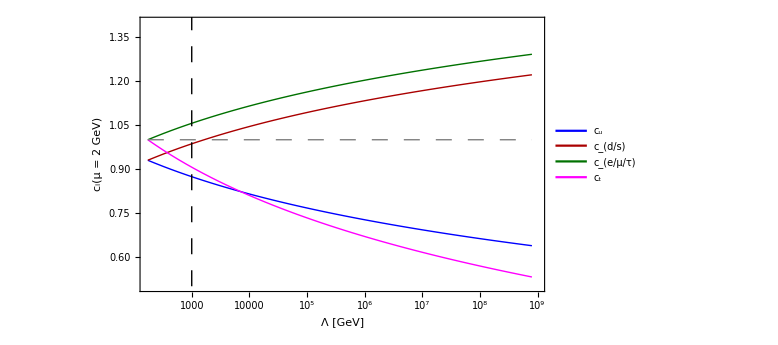

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\RG-flow.pdf

```mathematica
(*Cross-check: comparison with numeric expression from https://arxiv.org/pdf/2110.10698.pdf*)
ScaleNeubert=4*Pi*10^3;
posct=Position[ALPcouplingslist,"ct"][[1]][[1]];
ct1=Quiet[ALPcouplingsRGflow["Fermion universal",ScaleNeubert][[posct]]];
ct2=Quiet[ALPcouplingsRGflow["Gluon",ScaleNeubert][[posct]]];
ct3=Quiet[ALPcouplingsRGflow["W",ScaleNeubert][[posct]]];
(*Expression for Subscript[c, t] from Neubert's 2021 paper for Λ = 4π Tev*)
cttSolNeubert[cG_,cW_,cB_,cq_,cl_]=0.826*cq-1/2*10^-3(6.17*cΛ["cG",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+0.23*cΛ["cW",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+0.02cΛ["cB",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]);
{{"Benchmark","c_t = 1, other = 0", "c_G = 1, other = 0","c_W  = 1, other = 0"},{"c_t(μ_ω), this notebook",ct1,ct2,ct3},{"c_t(μ_ω), Neubert",cttSolNeubert[0,0,0,1,0],cttSolNeubert[1,0,0,0,0],cttSolNeubert[0,1,0,0,0]}}//TableForm
Print["Effect of the RG flow:"]
ModelTest="Fermion universal";
Λtest=10^5;
{Join[{"Coupling"},ALPcouplingslist],Join[{Row[{"Model ", ModelTest,", values at Λ = ",Λtest, " GeV"}]//ToString},couplingPatternOverall[ModelTest]],Join[{"Value below the EW scale"},ALPcouplingsRGflow["Fermion universal",Λtest]]}
(*Precomputed values of the ALP couplings at the RG scale μ = 2 GeV for the reference models and scales Λ*)
(*Plot*)
plotrg=Show[LogLinearPlot[{cRGval["Fermion universal",Λ,"cu"],cRGval["Fermion universal",Λ,"cd"],cRGval["Fermion universal",Λ,"ce"],cRGval["Fermion universal",Λ,"ct"],1},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Blue},{Thick, Darker@Red},{Thick,Darker@Darker@Green},{Thick,Magenta},{Thick,Gray,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Darker@Green,Dashing[0.02]},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}(*,PlotLabel->Style[Row[{"Universal fermion coupling"}],22,Black]*),Filling->{7->{Bottom,Directive[Gray,Opacity[0.3]]},8->{Bottom,Directive[Gray,Opacity[0.3]]},9->{Bottom,Directive[Gray,Opacity[0.3]]}},AspectRatio->0.6],LogLinearPlot[{100,100},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Blue},{Thick, Darker@Red}},PlotLegends->Placed[Style[#,22]&/@Join[{"c_u","c_(d/s)"}],{0.2,0.1}],Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}],LogLinearPlot[{100,100},{Λ,MASS["t"],8*10^8},PlotStyle->{{Thick,Darker@Darker@Green},{Thick,Magenta}},PlotLegends->Placed[Style[#,22]&/@Join[{"c_(e/μ/τ)","c_t"}],{0.35,0.1}],Frame-> True,FrameLabel->{"Λ [GeV]" , "c_i(μ = 2 GeV)"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{0.5,1.4}}],ListLogLinearPlot[Table[{10^3,a},{a,0.5,1.5,0.1}],Joined->True,PlotStyle->{{Thick,Black,Dashing[0.02]}}]]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"plots/RG-flow.pdf"}],plotrg]
```

## Running of FCNC couplings

### Definitions

```mathematica
{ItIntegrandCoef["cG",μ_],ItIntegrandCoef["cW",μ_],ItIntegrandCoef["cB",μ_]}={(4 αSsol[μ]^2)/(3 Pi^2),(3 αSU2Lsol[μ]^2)/(8 Pi^2),(17 αUYsol[μ]^2)/(72 Pi^2)};
keysIT=Keys[DownValues@ItIntegrandCoef][[All,1,1]]//DeleteDuplicates;
Vtb=1;
Vts=41.5*10^-3.;
Vtd=8*10^-3;
{CKMsuppression["b->s"],CKMsuppression["b->d"],CKMsuppression["s->d"]}={Vtb*Vts,Vtb*Vtd,Vts*Vtd};
FCNCtransitions=Keys[DownValues@CKMsuppression][[All,1,1]];
xtv=MASS["t"]^2/80^2.;
cosθW=80/91.;
FCNCcouplingTemp[model_,Λ_]:=Block[{},
Do[value[ALPcouplingslist[[i]]]=couplingPattern[model,ALPcouplingslist[[i]]],{i,1,Length[ALPcouplingslist],1}];
soltemp=NDSolve[Flatten[Table[{μ*D[RunningCoupling[coef,μ],μ]==cXXrunning[coef,μ],RunningCoupling[coef,Λ]==cΛ[coef,value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]},{coef,{"ct","cB","cW","cG"}}]],Evaluate[#[[0]]&/@couplingsList[μ]],{μ,MASS["t"],Λ}][[1]];
Do[runningSol[coef]=(RunningCoupling[coef,μ][[0]]/.soltemp),{coef,coefskeys}];
integrandIt[μ_]=1/μ(1-Exp[-18*Uval[MASS["t"],μ]])Sum[runningSol[coef][μ]*ItIntegrandCoef[coef,μ],{coef,keysIT}];
integralIt=-2/3(1-Exp[-18*Uval[MASS["t"],Λ]])2*runningSol["ct"][Λ]-NIntegrate[integrandIt[μ],{μ,Λ,MASS["t"]}];
-(1/6 integralIt+(4*Pi*αTsol[MASS["t"]])/(16 Pi^2)*(2*runningSol["ct"][MASS["t"]]*(1/4+3/2(1-xtv+Log[xtv])/(1-xtv)^2)+(3(1/137))/(2*Pi(1-cosθW^2))*cΛ["cW",value["cG"],value["cW"],value["cB"],value["cu"],value["cd"],value["cs"],value["cc"],value["cb"],value["ct"],value["ce"],value["cμ"],value["cτ"]]*(1-xtv+xtv*Log[xtv])/(1-xtv)^2))]
```

### RG flow computation/importing

```mathematica
fileFCNCcouplings=FileNameJoin[{NotebookDirectory[]//ParentDirectory,"Temporary data/FCNCcouplings.m"}];
If[!FileExistsQ[fileFCNCcouplings],
Do[
FCNCcouplingList[model]=ParallelTable[{Λ,Quiet[FCNCcouplingTemp[model,Λ]]},{Λ,ΛlistInt}];
Do[FCNCcoupling[transition,model,Λ_]=CKMsuppression[transition]*Interpolation[FCNCcouplingList[model],InterpolationOrder->1][Λ];
cij[transition,model,Λ_,fa_]=1/fa FCNCcoupling[transition,model,Λ]*If[transition!="s->d",MASS["b"],MASS["s"]] 1/2;
,{transition,FCNCtransitions}];
,{model,ModelListAll}];
TableExportFCNCcouplings=Flatten[Table[{transition,model,FCNCcoupling[transition,model,Λ],cij[transition,model,Λ,fa]},{transition,FCNCtransitions},{model,ModelListAll}],1];
Export[fileFCNCcouplings,TableExportFCNCcouplings,"MX"]
,
TableImportFCNCcouplings=Import[fileFCNCcouplings,"MX"];
Do[
tran=TableImportFCNCcouplings[[i]][[1]];
mod=TableImportFCNCcouplings[[i]][[2]];
{FCNCcoupling[tran,mod,Λ_],cij[tran,mod,Λ_,fa_]}=Drop[TableImportFCNCcouplings[[i]],2],{i,1,Length[TableImportFCNCcouplings],1}];
]
```

### Plots and cross-checks

Coupling pattern | c_q = 1, c_l = 0, c_GG = 0, c_W = 0 | c_q = 0, c_l = 0, c_GG = 1, c_W = 0 | c_q = 0, c_l = 0, c_GG = 0, c_W = 1
c_bs, this notebook | 0.00163929 | -2.44798×10^-6 | -1.09814×10^-6
c_bs, Neubert | 0.00155662 | -2.5315×10^-6 | -1.162×10^-6

(Transition i->j | ALP model | scale Λ | |C_ij| f_a = 1. PeV)
b->d | B | 1 TeV | 1.64104×10^-15
b->d | Fermion universal | 1 TeV | 3.44463×10^-10
b->d | Gluon | 1 TeV | 2.70586×10^-13
b->d | Gluon 1811.03474 | 1 TeV | 1.35293×10^-13
b->d | Quark universal | 1 TeV | 3.45156×10^-10
b->d | W | 1 TeV | 4.57528×10^-13
b->d | B | EW | 3.1588×10^-32
b->d | Fermion universal | EW | 5.63141×10^-12
b->d | Gluon | EW | 6.84244×10^-30
b->d | Gluon 1811.03474 | EW | 3.39012×10^-30
b->d | Quark universal | EW | 4.9592×10^-12
b->d | W | EW | 4.48137×10^-13
b->d | B | Neubert | 9.37085×10^-15
b->d | Fermion universal | Neubert | 7.41831×10^-10
b->d | Gluon | Neubert | 1.10896×10^-12
b->d | Gluon 1811.03474 | Neubert | 5.54482×10^-13
b->d | Quark universal | Neubert | 7.42619×10^-10
b->d | W | Neubert | 4.97472×10^-13
b->s | B | 1 TeV | 8.51291×10^-15
b->s | Fermion universal | 1 TeV | 1.7869×10^-9
b->s | Gluon | 1 TeV | 1.40366×10^-12
b->s | Gluon 1811.03474 | 1 TeV | 7.01831×10^-13
b->s | Quark universal | 1 TeV | 1.7905×10^-9
b->s | W | 1 TeV | 2.37343×10^-12
b->s | B | EW | 1.63863×10^-31
b->s | Fermion universal | EW | 2.92129×10^-11
b->s | Gluon | EW | 3.54951×10^-29
b->s | Gluon 1811.03474 | EW | 1.75862×10^-29
b->s | Quark universal | EW | 2.57259×10^-11
b->s | W | EW | 2.32471×10^-12
b->s | B | Neubert | 4.86113×10^-14
b->s | Fermion universal | Neubert | 3.84825×10^-9
b->s | Gluon | Neubert | 5.75275×10^-12
b->s | Gluon 1811.03474 | Neubert | 2.87638×10^-12
b->s | Quark universal | Neubert | 3.85234×10^-9
b->s | W | Neubert | 2.58064×10^-12
s->d | B | 1 TeV | 1.35337×10^-18
s->d | Fermion universal | 1 TeV | 2.84079×10^-13
s->d | Gluon | 1 TeV | 2.23152×10^-16
s->d | Gluon 1811.03474 | 1 TeV | 1.11576×10^-16
s->d | Quark universal | 1 TeV | 2.84651×10^-13
s->d | W | 1 TeV | 3.77324×10^-16
s->d | B | EW | 2.60507×10^-35
s->d | Fermion universal | EW | 4.64423×10^-15
s->d | Gluon | EW | 5.64297×10^-33
s->d | Gluon 1811.03474 | EW | 2.79584×10^-33
s->d | Quark universal | EW | 4.08986×10^-15
s->d | W | EW | 3.69579×10^-16
s->d | B | Neubert | 7.72816×10^-18
s->d | Fermion universal | Neubert | 6.11789×10^-13
s->d | Gluon | Neubert | 9.14565×10^-16
s->d | Gluon 1811.03474 | Neubert | 4.57283×10^-16
s->d | Quark universal | Neubert | 6.1244×10^-13
s->d | W | Neubert | 4.10266×10^-16)

(b->d | Fermion universal | 1 TeV | 3.44463×10^-10
b->s | Fermion universal | 1 TeV | 1.7869×10^-9
s->d | Fermion universal | 1 TeV | 2.84079×10^-13
b->d | Fermion universal | EW | 5.63141×10^-12
b->s | Fermion universal | EW | 2.92129×10^-11
s->d | Fermion universal | EW | 4.64423×10^-15)

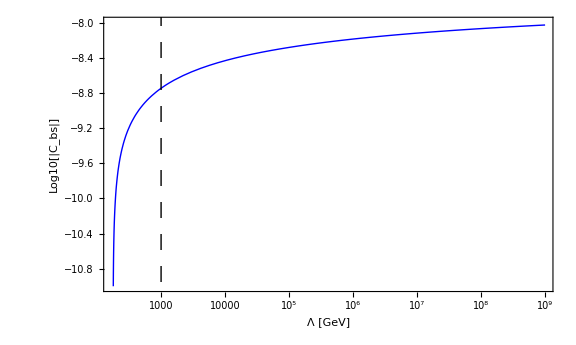

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALP phenomenology\plots\cbs-flow.pdf

```mathematica
(*Cross-check: comparison with numeric expression from https://arxiv.org/pdf/2110.10698.pdf*)
FCNCcouplingNeubert4PiTeV[transition_,cq_,cG_,cl_,cW_,cB_]:=CKMsuppression[transition]*(0.019*2*cq-6.1*10^-5 cΛ["cG",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]-2.8*10^-5 cΛ["cW",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl]+1.8*10^-7 cΛ["cB",cG,cW,cB,cq,cq,cq,cq,cq,cq,cl,cl,cl])
{{"Coupling pattern","c_q = 1, c_l = 0, c_GG = 0, c_W = 0","c_q = 0, c_l = 0, c_GG = 1, c_W = 0","c_q = 0, c_l = 0, c_GG = 0, c_W = 1"},{"c_bs, this notebook",FCNCcoupling["b->s","Quark universal",ScaleNeubert],FCNCcoupling["b->s","Gluon",ScaleNeubert],FCNCcoupling["b->s","W",ScaleNeubert]},{"c_bs, Neubert",FCNCcouplingNeubert4PiTeV["b->s",1,0,0,0,0],FCNCcouplingNeubert4PiTeV["b->s",0,1,0,0,0],FCNCcouplingNeubert4PiTeV["b->s",0,0,0,1,0]}}//TableForm
faval=10^6.;
ttt=Flatten[Table[{transition,model,scale,Abs[cij[transition,model,scaleVal[scale],faval]]},{transition,FCNCtransitions},{scale,scaleKeys},{model,ModelListAll}],{1,2,3}];
Join[{{"Transition i->j","ALP model","scale Λ","|C_ij| f_a = " <>ToString[10^-6. faval]<>" PeV)"}},ttt]
SortBy[Select[ttt,#[[2]]=="Fermion universal"&&#[[3]]!="Neubert"&],#[[3]]&]
PlotcbsFlow=Show[LogLinearPlot[{Log10[cij["b->s","Fermion universal",Λ,faval]]},{Λ,MASS["t"],10^9},PlotStyle->{{Thick,Blue},{Thick,Gray,Dashing[0.02]},{Thickness[0.002],Lighter@Blue},{Thick,Darker@Red},{Thickness[0.002],Lighter@Red},{Thickness[0.002],Lighter@Red},{Thick,Darker@Darker@Green},{Thickness[0.002],Lighter@Green},{Thickness[0.002],Lighter@Green},{Thick,Cyan},{Thick,Magenta},{Thick,Purple},{Thick,Black,Dashing[0.02]},{Thick,Blue},{Thickness[0.003],Gray,Dashing[0.01]},{Thick, Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Orange,Dashing[0.02]},{Thick,Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Purple,Dashing[0.02]},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]}},Frame-> True,FrameLabel->{"Λ [GeV]" , "Log10[|C_bs|]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{MinMax[ΛlistInt],{-11,-8}},Filling->{2->{{3},Directive[Blue,Opacity[0.1]]},5->{{6},Directive[Red,Opacity[0.1]]},8->{{9},Directive[Green,Opacity[0.1]]}}(*,PlotLabel->Style[Row[{"c_q = c_l = 1, f = 1 TeV"}],22,Black]*),AspectRatio->0.6],ListLogLogPlot[Table[{10^3,10^x},{x,-99,99,0.1}],Joined->True,PlotStyle->{{Thick,Black,Dashing[0.02]}}]]
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory,"plots/cbs-flow.pdf"}],PlotcbsFlow]
```